```mathematica
file1[[1,5]]
```

{0.49986,0.450668,0.0340416,0.00139472,0.00303663,0.0109991}

```mathematica
a=file1[[1,4,9]]
```

{{0,-0.192998,0,-0.0864289,-0.977385,0},{-0.116,0.944577,0.241026,0.024758,-0.188709,0.000834071},{-0.138395,-0.245411,0.914744,0.101325,0.0394998,0.268395},{0.617084,-0.000524424,0.225819,0.438627,-0.0386837,-0.611819},{0.442504,0.0395755,0.20072,-0.864235,0.0686085,-0.103566},{0.625131,0.0934509,-0.117757,0.205801,-0.0366518,0.736827}}

```mathematica
funij[i_,j_]:=(Cos@ArcTan@file1[[;;,2,8]](file1[[;;,4,9,j,2]]+I file1[[;;,4,9,j,5]])/Sqrt@2
-Sin@ArcTan@file1[[;;,2,8]](file1[[;;,4,9,j,1]]+I file1[[;;,4,9,j,4]])/Sqrt@2)(file1[[;;,4,9,i,3]]+I file1[[;;,4,9,i,6]])
```

```mathematica
gHHZ[i_,j_]:=Power[Abs[funij[i,j]-funij[j,i]],2]
```

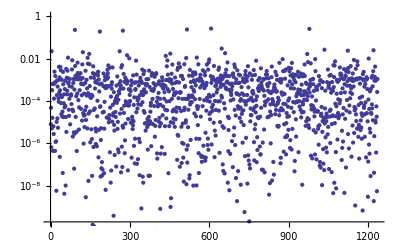

```mathematica
ListLogPlot@gHHZ[1,2]
```